```mathematica
imgs=RemoveBackground[#,{Black,0.05}]&/@(ConformImages[ImageTrim[#,First[Flatten@Values[ImageBoundingBoxes[#]]]]&/@{-Graphics-,-Graphics-,-Graphics-}])
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
mask=Erosion[Binarize[imgs[[2]],0],1];
```

```mathematica
parallaxL=First@ImageDisplacements[imgs[[{2,1}]]];
parallaxR=First@ImageDisplacements[imgs[[{2,3}]]];
parallax=parallaxL-parallaxR;
```

```mathematica
depth=Blur@Opening[ImageMultiply[ImageAdjust@Image[parallax[[All,All,1]]],mask],DiskMatrix[4]];
depthFunction=ListInterpolation[Transpose@Reverse@ImageData[depth]];
```

```mathematica
resolution=ImageAdjust@ImageSaliencyFilter[imgs[[2]]];
resolutionFunction=ListInterpolation[Transpose@Reverse@ImageData@resolution];
```

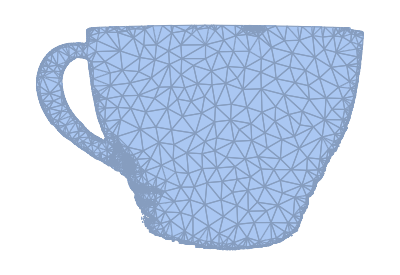

```mathematica
Ω=TriangulateMesh[ImageMesh[Erosion[mask,DiskMatrix[2]]],MeshRefinementFunction->Function[{vertices,area},area>32+512 (1-resolutionFunction@@Mean[vertices])^6]]
```

```mathematica
Graphics3D[GraphicsComplex[Apply[{##,depthFunction[##]}&,MeshCoordinates[Ω],{1}],{EdgeForm[],MeshCells[Ω,2]}],PlotRange->Append[Thread[{0,ImageDimensions[mask]}],{0,1}],BoxRatios->{1,1,2/3},ViewPoint->Top]
```

-Graphics3D-

```mathematica
texture=SetAlphaChannel[imgs[[2]],mask]
```

-Graphics-

```mathematica
Graphics3D[{Texture[texture],GraphicsComplex[Apply[{##,depthFunction[##]}&,MeshCoordinates[Ω],{1}],{EdgeForm[],MeshCells[Ω,2]},VertexTextureCoordinates->Map[#/ImageDimensions[texture]&,MeshCoordinates[Ω]]]},PlotRange->Append[Thread[{0,ImageDimensions[mask]}],{0,1}],BoxRatios->{1,1,2/3},Lighting->{{"Ambient",White}},ViewPoint->Top,Boxed->False]
```

-Graphics3D-